```mathematica
<<Radia`;
```

Radia Version: 4.32 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(*MOT geometry*)
MOTIR= 56; (*mm*)
Epoxy=0;(*mm epoxy thickness*)
NumTurns = 4;(*turns per layer*)
MOTI =1;(*A*)(****************play with this***************************)
CoilOut = 4.2;(*mm*)
CoilIn = 1.8;(*mm*)
MOTOR = MOTIR+NumTurns*CoilOut ;(*mm*)
MOTJ = MOTI/((CoilOut)^2); (*A/mm2*)
NumLayers =2;
height =NumLayers*CoilOut; (*mm*)
sep = 55;(*mm near-Holmholtz*); (****************play with this***************************)
Distance=sep+height;
Radius = (MOTIR+MOTOR)/2;
lx=0;(*mm lengths of straight parts long x-axis of the racetrack*)
ly=0;(*mm lengths of straight parts long y-axis of the racetrack*)
(* angle of coils viewed projected onto the z-x plane. Amount of rotation about the y-axis*)
(*theta = 0* 180/π;*)
(*Create coils using radia*)
(*Keep the difference of Helmholtz and anti-Helmholtz in mind when you create coils!*)
topcoil=radObjRaceTrk[{0,0,Distance/2},{MOTIR,MOTOR},{lx,ly},height,100,MOTJ];
radTrfOrnt[topcoil,radTrfRot[{0,0,0},{0,1,0},π/2]];
bottomcoil=radObjRaceTrk[{0,0,Distance/2},{MOTIR,MOTOR},{lx,ly},height,100,MOTJ];
radTrfOrnt[bottomcoil,radTrfRot[{0,0,0},{0,1,0},-π/2]];
MOT=radObjCnt[{topcoil,bottomcoil}];
(*Draw graphical representation*)
MOTDR=radObjDrw[MOT];
Show[Graphics3D[MOTDR],Axes->True]

(*I think that the y-axis is through the center of the coils?*)
(* plot results *)
rmax = 200;
numpts = 500;
(* center of coordinates *)
xcenter =0;
ycenter =1;
zcenter =0;
BZoffset = 0; (*G*)

MOTIR+NumTurns*CoilOut/2-height/2(*mm exact Holmholtz*)
sep
Distance
NumTurns*CoilOut
NumLayers*CoilOut
```

-Graphics3D-

60.2

55

63.4

16.8

8.4

```mathematica
MOTOR
```

72.8

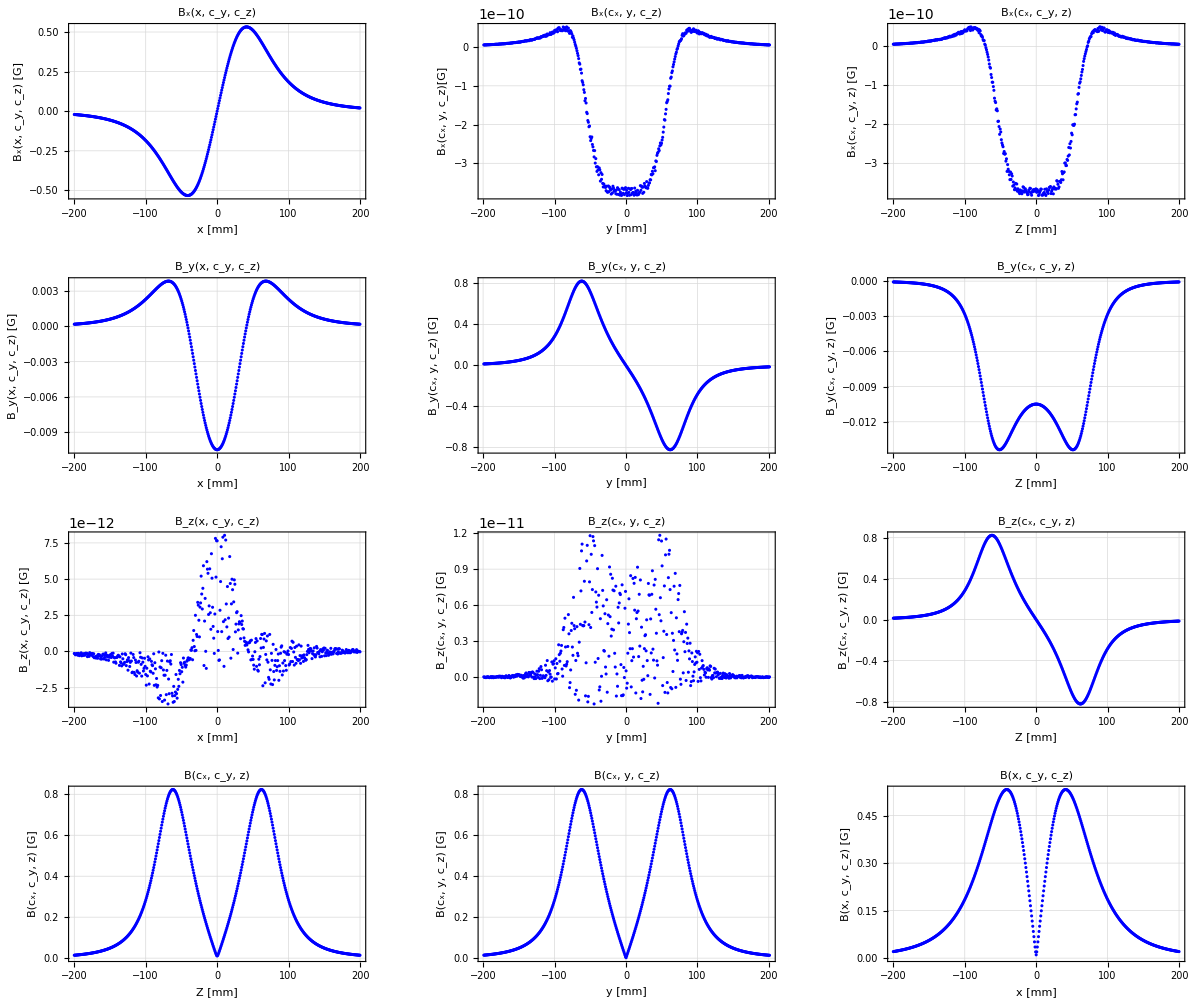

```mathematica
(*Bz*)
BzZaxis=Table[{z,BZoffset + 10^4*radFld[MOT,"Bz",{xcenter, ycenter,z}]},{z,zcenter-rmax,zcenter + rmax, 2*rmax/numpts}];
BzYaxis = Table[{y,BZoffset +10^4*radFld[MOT,"Bz",{xcenter,y, zcenter}]},{y,ycenter-rmax,ycenter+rmax,2*rmax/numpts}];
BzXaxis = Table[{x, BZoffset +10^4 * radFld[MOT, "Bz", {x, ycenter, zcenter}]}, {x, xcenter-rmax, xcenter+rmax, 2*rmax/numpts}];
BzZplot=ListPlot[BzZaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [mm]","B_z(c_x, c_y, z) [G]"},PlotLabel->"B_z(c_x, c_y, z)",PlotStyle->{Blue}];
BzYplot = ListPlot[BzYaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [mm]","B_z(c_x, y, c_z) [G]"},PlotLabel->"B_z(c_x, y, c_z)",PlotStyle->{Blue}];
BzXplot = ListPlot[BzXaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [mm]","B_z(x, c_y, c_z) [G]"},PlotLabel->"B_z(x, c_y, c_z)",PlotStyle->{Blue}];
(*GraphicsRow[{BzXplot, BzYplot, BzZplot}, PlotLabel->"B_z Field"]*)
(*Bx*)
BxZaxis=Table[{z,10^4*radFld[MOT,"Bx",{xcenter,ycenter,z}]},{z,zcenter-rmax,zcenter +rmax, 2*rmax/numpts}];
BxYaxis = Table[{y,10^4*radFld[MOT,"Bx",{xcenter,y,zcenter}]},{y,ycenter-rmax,ycenter+rmax,2*rmax/numpts}];
BxXaxis = Table[{x, 10^4 * radFld[MOT, "Bx", {x, ycenter, zcenter}]}, {x, xcenter-rmax, xcenter+rmax, 2*rmax/numpts}];
BxZplot=ListPlot[BxZaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [mm]","B_x(c_x, c_y, z) [G]"},PlotLabel->"B_x(c_x, c_y, z)",PlotStyle->{Blue}];
BxYplot = ListPlot[BxYaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [mm]","B_x(c_x, y, c_z)[G]"},PlotLabel->"B_x(c_x, y, c_z)",PlotStyle->{Blue}];
BxXplot = ListPlot[BxXaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [mm]","B_x(x, c_y, c_z) [G]"},PlotLabel->"B_x(x, c_y, c_z)",PlotStyle->{Blue}];
(*GraphicsRow[{BxXplot, BxYplot, BxZplot}, PlotLabel->"B_xField"]*)
(*By*)
ByZaxis=Table[{z,10^4*radFld[MOT,"By",{xcenter,ycenter,z}]},{z,zcenter-rmax,zcenter+rmax, 2*rmax/numpts}];
ByYaxis = Table[{y,10^4*radFld[MOT,"By",{xcenter,y,zcenter}]},{y,ycenter-rmax,ycenter+rmax,2*rmax/numpts}];
ByXaxis = Table[{x, 10^4 * radFld[MOT, "By", {x, ycenter, zcenter}]}, {x, xcenter-rmax, xcenter+rmax, 2*rmax/numpts}];
ByZplot=ListPlot[ByZaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [mm]","B_y(c_x, c_y, z) [G]"}, PlotLabel->"B_y(c_x, c_y, z)", PlotStyle->{Blue}];
ByYplot = ListPlot[ByYaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [mm]","B_y(c_x, y, c_z) [G]"},PlotLabel->"B_y(c_x, y, c_z)", PlotStyle->{Blue}];
ByXplot = ListPlot[ByXaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [mm]","B_y(x, c_y, c_z) [G]"},PlotLabel->"B_y(x, c_y, c_z)", PlotStyle->{Blue}];
(*|B|*)
BZaxis = Table[{z, Sqrt[Total[( {0, 0, BZoffset}  + 10^4 * radFld[MOT, "B", {xcenter, ycenter, z}] )^2]]}, {z,zcenter-rmax,zcenter+rmax, 2*rmax/numpts}];
BYaxis = Table[{y,Sqrt[Total[( {0, 0, BZoffset}  + 10^4 * radFld[MOT, "B", {xcenter,y, zcenter}] )^2]]}, {y, ycenter-rmax, ycenter+rmax, 2*rmax/numpts}];
BXaxis = Table[{x,Sqrt[Total[( {0, 0, BZoffset}  + 10^4 * radFld[MOT, "B", {x,ycenter, zcenter}] )^2]]}, {x, xcenter-rmax, xcenter+rmax, 2*rmax/numpts}];
BZplot=ListPlot[BZaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [mm]","B(c_x, c_y, z) [G]"}, PlotLabel->"B(c_x, c_y, z)", PlotStyle->{Blue}];
BYplot = ListPlot[BYaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [mm]","B(c_x, y, c_z) [G]"},PlotLabel->"B(c_x, y, c_z)", PlotStyle->{Blue}];
BXplot = ListPlot[BXaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [mm]","B(x, c_y, c_z) [G]"},PlotLabel->"B(x, c_y, c_z)", PlotStyle->{Blue}];

(*GraphicsRow[{ByXplot, ByYplot, ByZplot}, PlotLabel->"B_y Field"]*)
GraphicsGrid[{{BxXplot, BxYplot, BxZplot}, {ByXplot, ByYplot, ByZplot}, {BzXplot, BzYplot, BzZplot}, {BZplot, BYplot, BXplot}}, PlotLabel->"MOT Fields", Frame->True, ImageSize->Full]

dist =  N[Table[z,{z,zcenter-rmax,zcenter +rmax, 2*rmax/numpts}]];
Bxx = Table[10^4*radFld[MOT,"Bx",{x,ycenter,zcenter}],{x,xcenter-rmax,xcenter+rmax,2*rmax/numpts}];
Byy = Table[10^4*radFld[MOT,"By",{xcenter,y,zcenter}],{y,ycenter-rmax,ycenter+rmax,2*rmax/numpts}];
Bzz = Table[10^4*radFld[MOT,"Bz",{xcenter,ycenter,z}],{z,zcenter-rmax,zcenter+rmax,2*rmax/numpts}];
(*Export["//128.112.86.75//lithium//Simulation//Magnet Coils//MOT Coils//Mot_fields.tsv",Transpose[{dist, Bxx,Byy,Bzz}]];*)
```

```mathematica
(* water cooling estimates*)
LperLayer = 0;
For[n=0,n<NumTurns,n++,LperLayer=LperLayer+2*Pi*(MOTIR+CoilOut*n)];
Ltotal=0.001*(LperLayer*NumLayers)+0.86+0.89; (*L for entire MOT coil: 2 coils each with 4 layers and each layer with 6 turns + 12 leads of 0.5m each*)
(*Ltotal =0.001*(196.4*Pi*8+2*0.6);(*2*((LperLayer*0.001))+1.2*)
(*m and also 1.2m length of extra coils*)*)
RhoCopper = 1.68*10^(−8);(*in Ohm-m*)
CrossSection = ((CoilOut-Epoxy)^2-CoilIn^2)*10^(-6);
Rho=RhoCopper/CrossSection;
pipeDiaIn=CoilIn*39.3701*0.001;(*pipe inner diameter in inch*)
```

```mathematica
pdissipated=Rho*MOTI^2*Ltotal (*in W*)
```

0.00569513

```mathematica
V=pdissipated/MOTI
PressureDrop=80(*psi*);
```

0.00569513

```mathematica
flowRateGal =((PressureDrop*140^1.85*(pipeDiaIn)^4.87)/(4.52*(Ltotal*3.28084)))^0.54(*in Gal/min*)
```

0.139414

```mathematica
0.13941441536524374
```

0.139414

```mathematica
flowRate=flowRateGal/0.000264172;(*convert GPM to mL/min*)
```

```mathematica
deltaT=14.3*pdissipated/flowRate (*in deg C*)
```

0.000154319

```mathematica
BzZaxis;
```

```mathematica
BxXaxis;
```

```mathematica
BzZaxis=Table[{z,BZoffset + 10^4*radFld[MOT,"Bz",{xcenter, ycenter,z}]},{z,zcenter-rmax,zcenter + rmax, 2*rmax/numpts}];
```

```mathematica
Length[BzZaxis]
```

501

```mathematica
subsetz=Take[BzZaxis,{245,255}];
```

```mathematica
BzZaxis;
subsetx=Take[BxXaxis,{245,255}];
subsety=Take[ByYaxis,{245,255}];
```

```mathematica
ParabolaX=Fit[subsetx,{1,x,x^2},x]
```

-0.0000473862+0.0209363 x+0.000013222 x^2

```mathematica
(*Uniformity among Y-Z plane*)
subsetxY=Take[BxYaxis,{245,255}];
ParabolaXY=Fit[subsetxY,{1,y,y^2},y]
subsetxZ=Take[BxZaxis,{245,255}];
ParabolaXZ=Fit[subsetxZ,{1,z,z^2},z]
```

-3.72097×10^-10-5.41674×10^-14 y-1.15939×10^-13 y^2

-3.68428×10^-10-1.58104×10^-12 z-5.03343×10^-13 z^2

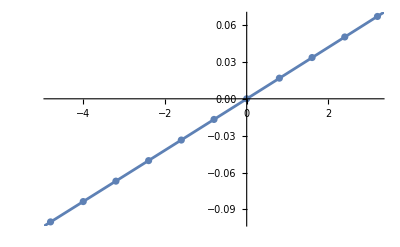

```mathematica
Show[ListPlot[subsetx],Plot[ParabolaX,{x,-15,15}]]
```

```mathematica
164/30.5
```

5.37705

```mathematica
ParabolaY=Fit[subsety,{1,x,x^2},x]
```

4.69853×10^-6-0.0105134 x-1.24169×10^-6 x^2

```mathematica
ParabolaZ=Fit[subsetz,{1,x,x^2},x]
```

-0.0000178035-0.0105118 x+4.96735×10^-6 x^2

```mathematica
16.40031967814099/2
```

8.20016

```mathematica
8.5*2
```

17.